## Белко Владислав, ПО-5

Лабораторная работа №8.

### DatabaseReference[]

DatabaseReference - подключение к БД

```mathematica
BVlab=DatabaseReference[<|
"Backend"->"MySQL",
"Name"->"course",
"Port"->Automatic,
"Host"->"localhost",
"Username"->"root",
"Password"->"admin"
|>]
```

DatabaseReference[…]

### DatabaseConnect[ref]

DatabaseConnect - проверка успешности подключения к базе данных

```mathematica
DatabaseConnect[BVlab]
```

Success[…]

### ref[“Connected”]

DatabaseReference[]["Connected"] - убедиться, что подключены к БД

```mathematica
BVlab["Connected"]
```

True

### ref[{"Username", "Password", "Host", "Port", "Backend", "Name"}]

DatabaseReference[][{"Username", "Password", "Host", "Port", "Backend", "Name"}] - получить определеные свойства подключения

```mathematica
BVlab[{"Username", "Password","Host", "Port", "Backend", "Name"}]
```

<|Username→root,Password→admin,Host→localhost,Port→None,Backend→MySQL,Name→course|>

### RelationalDatabase[ref]

RelationalDatabase - посмотреть какие таблицы есть в БД

```mathematica
RelationalDatabase[BVlab]
```

RelationalDatabase[…]

### EntityStore[ref], EntityStores[]

EntityStore[ref] - создаем хранилище
EntityRegister[store] - без этой функции не будет работать EntityValue
EntityStores[] - вывести хранилища

```mathematica
BVlabStore=EntityStore[BVlab]
```

EntityStore[…]

```mathematica
lstTables = EntityRegister[BVlabStore]
```

{сп_орг,сп_произв,таблчасть_номенкл,сп_должсотр,сп_номенкл,оп_инвенопис,таблчасть_состком,оп_приказсоздкоминвент,сп_сотр,сп_местхран,сп_едхран,коминвент}

```mathematica
EntityStores[]
```

{EntityStore[…]}

### EntityValue[“таблица”, “EntityCount”]

EntityValue["таблица", "EntityCount"] - определяет количество записей в таблице

```mathematica
lst={{"Таблица", "Количество строк"}};
For[i=1, i<Length[lstTables],i++,
lst=Join[lst,{{lstTables[[i]],EntityValue[lstTables[[i]],"EntityCount"]}} ]
]

Grid[lst,Frame->All,Alignment->Left]
```

Таблица | Количество строк
сп_орг | 1
сп_произв | 1
таблчасть_номенкл | 2
сп_должсотр | 3
сп_номенкл | 1
оп_инвенопис | 1
таблчасть_состком | 1
оп_приказсоздкоминвент | 1
сп_сотр | 6
сп_местхран | 1
сп_едхран | 1

```mathematica
Print["Создано приказов о проведении инвентаризационной комиссии: ", EntityValue["оп_приказсоздкоминвент", "EntityCount"]]
```

Создано приказов о проведении инвентаризационной комиссии: 1

```mathematica
Print["Зарегистрировано должностей сотрудников: ", EntityValue["сп_должсотр", "EntityCount"]]
```

Зарегистрировано должностей сотрудников: 3

```mathematica
Print["Количество участников в инвентаризационной комиссии: ", EntityValue["таблчасть_состком", "EntityCount"]]
```

Количество участников в инвентаризационной комиссии: 1

```mathematica
Print["Проведено инвентаризационных комиссий: ", EntityValue["коминвент", "EntityCount"]]
```

Проведено инвентаризационных комиссий: 1

```mathematica
Print["Количество зарегистрированных мест хранения: ", EntityValue["сп_местхран", "EntityCount"]]
```

Количество зарегистрированных мест хранения: 1

```mathematica
Print["Количество утверждено единиц хранения: ", EntityValue["сп_едхран", "EntityCount"]]
```

Количество утверждено единиц хранения: 1

### EntityValue[] --> используя SELECT - FROM - INNER JOIN ON

Объединить таблицу Сотрудники, Должность сотрудника  и вывести поля таблиц в список Wolframe Mathematica

```mathematica
(*
SELECT
sotr.Наим, sotr.КодСотр
FROM
сп_сотр AS sotr
INNER JOIN сп_должсотр AS job ON job.КодДолжСотр=sotr.КодДолжСотр
*)
EntityValue[
CombinedEntityClass[
"сп_должсотр",(*FROM сп_должсотр*)
"сп_сотр",(*FROM сп_сотр*)
EntityFunction[{job, sotr},
(*
  FROM FROM сп_должсотр AS job
INNER JOIN сп_сотр AS sotr ON job.КодДолжСотр == sotr.КодДолжСотр
*)
job["КодДолжСотр"]==sotr["КодДолжСотр"]
]
],{
EntityProperty["сп_сотр", "Наим"],(*SELECT sotr.Наим*)
EntityProperty["сп_сотр", "КодСотр"],(*SELECT sotr.КодДолж*)
EntityProperty["сп_сотр", "КодДолжСотр"],(*SELECT sotr.КодДолжСотр*)
EntityProperty["сп_должсотр", "Наим"](*SELECT job.Наим*)
}]
```

{{Гук_Ирина_Анатольевна,1,1,Заведующий магазином},{Иванов Иван Иванович,2,2,Грузчик},{Алексеев Алексей Алексеевич,3,2,Грузчик},{Стасянов Стас Станиславович,4,3,Продавец},{Олегов Олег Олегович,5,3,Продавец},{Димов Дмитрий Дмитриевич,6,3,Продавец}}

```mathematica
TableForm[%21]
```

Гук_Ирина_Анатольевна | 1 | 1 | Заведующий магазином
Иванов Иван Иванович | 2 | 2 | Грузчик
Алексеев Алексей Алексеевич | 3 | 2 | Грузчик
Стасянов Стас Станиславович | 4 | 3 | Продавец
Олегов Олег Олегович | 5 | 3 | Продавец
Димов Дмитрий Дмитриевич | 6 | 3 | Продавец

```mathematica
jobs = EntityValue["сп_сотр", "КодДолжСотр"]
```

{1,2,2,3,3,3}

```mathematica
jobName = EntityValue["сп_должсотр","Наим"]
```

{Заведующий магазином,Грузчик,Продавец}

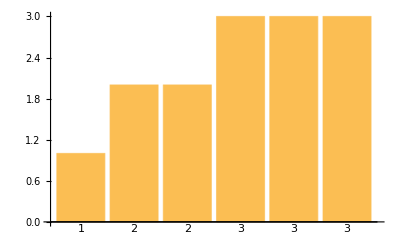

```mathematica
BarChart[jobs, ChartLabels->jobs]
```

где 1 - заведующий магазином, 2 - грузчик, 3 - продавец

### DatabaseDisconnect[ref]

DatabaseDisconnect[ref] - отключиться от базы данных

```mathematica
DatabaseDisconnect[BVlab]
```

Success[…]

Литература:
- https://reference.wolfram.com/language/guide/WorkingWithRelationalDatabases.html
- https://reference.wolfram.com/language/tutorial/RelationalDatabasesQuickStart.html#2047181595

### Wolfram Alpha в свободной форме - математические уравнения

WolframAlphaQueryParseResults

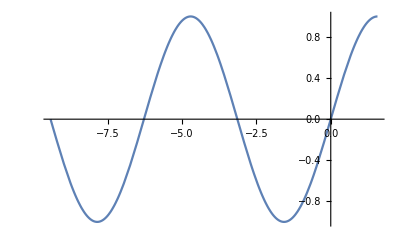

WolframAlphaQueryParseResults

1

### Wolfram Alpha - химические элементы

WolframAlphaQueryResults

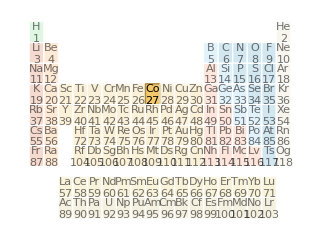

### Wolfram Alpha - цвет

WolframAlphaQueryResults

-Graphics-
(x, y values from xyY representation projected on to CIE 1931 xy chromaticity diagram)

### Wolfram Alpha - анатомия

skeleton model

WolframAlphaQueryResults

youtube.com visitors per day

WolframAlphaQueryResults

Wolfram Alpha. Загружено изображение. Работает только в онлайн-версии. При попытке загрузить изображение в Wolfram Mathematica выдаёт ошиьку 414

```mathematica
-Graphics-
-Graphics-
```